```mathematica
n=50;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,100}]];
AdjacencyGraph[k]*)
```

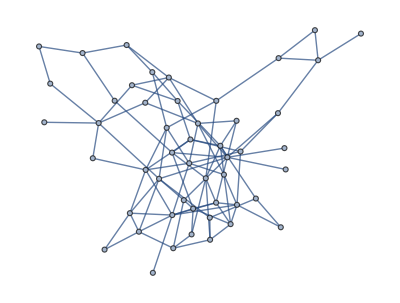
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<200>, {50, 50}]

```mathematica
data={-2.8439779401366865,-2.4976347915503685,0.016564321932995327,0.8393227737417376,2.1090576018415823,-2.3137925836711317,-2.400880057296099,1.914340141956699,-2.4491938544105554,-2.8361064382403613,2.288776710697519,-2.529021728470586,-0.16404297311049604,0.5680020542988005,-2.6297488075062203,-0.15957025979380293,2.3953330302474476,-1.5171818162141497,-1.7240312668200777,-0.8631106869173285,-2.9915946834875324,1.6642791767008398,-0.26800714802709447,0.43445289063646825,1.5821822956535607,2.075650332846416,2.921228113836319,1.631210999065217,-1.4470342034190338,-2.371344185073366,-2.3929403824336277,-0.16059514153483176,0.14635465800990413,-1.4443238319555303,1.5691732672888685,0.933942733124081,-2.265869277082809,-2.7941602809047956,2.9378949375021306,-1.0828771305678035,-2.4816407730509726,-0.31475493192845444,0.5634659764454392,1.7319901445637398,3.1312502984072696,-3.110447233720033,-1.3849804469612046,2.4910725131208227,-0.5294179483337293,-2.67354292006916};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,0],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==6-3/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
data2=Flatten[Table[Mod[Subscript[z,i][tt],2Pi],{i,1,n}]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,-7.27596×10^-12,0.,0.,0.,0.,0.}

{0.}

{0.0758595,0.0758595,3.21745,3.21745,4.78825,0.0758595,0.0758595,1.64666,0.0758595,3.21745,4.78825,4.78825,1.64666,3.21745,4.78825,1.64666,3.21745,0.0758595,1.64666,1.64666,4.78825,3.21745,1.64666,1.64666,4.78825,3.21745,4.78825,3.21745,0.0758595,4.78825,0.0758595,1.64666,1.64666,1.64666,3.21745,3.21745,0.0758595,4.78825,4.78825,1.64666,4.78825,1.64666,3.21745,3.21745,4.78825,4.78825,0.0758595,3.21745,1.64666,4.78825}

```mathematica
zvuk={1,1,3,3,4,1,1,2,1,3,4,4,2,3,4,2,3,1,2,2,4,3,2,2,4,3,4,3,1,4,1,2,2,2,3,3,1,4,4,2,4,2,3,3,4,4,1,3,2,4};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];
Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];
findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,60}],{i,1,n}];
```

```mathematica
Sound[Flatten[Table[Table[If[Round[a[[i]][[j]],0.05]==t,If[zvuk[[i]]==1,SoundNote["G",{t,t+0.1},"Vibraphone"],If[zvuk[[i]]==2,SoundNote["B",{t,t+0.1},"Vibraphone"],If[zvuk[[i]]==3,SoundNote["D",{t,t+0.1},"Vibraphone"],SoundNote["F",{t,t+0.1},"Vibraphone"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a[[i]]]}],{t,0,60,0.05}]],{0,80.066}]
```

```mathematica
Export["sim8_vibraphone.mp3",%29]
```

sim8_vibraphone.mp3

```mathematica
Export["MIDI_SM8.mid",%29]
```

MIDI_SM8.mid

```mathematica
granica=60;
```

```mathematica
video[t_]:=Grid[{{GraphPlot[SomeGraph,PlotStyle->{Gray,Thickness[0.004]},VertexRenderingFunction->({Hue[Rescale[lisboj[t][[Sequence@@#2]],{0,2Pi}]],Disk[#1,0.12]}&),ImageSize->700,PlotRangePadding->0],Show[{With[{sectors=360},angle=2 Pi/sectors;
Graphics[{Table[{Hue[i/sectors],EdgeForm[{Thick,Hue[i/sectors]}],Disk[{0,0},1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]],ListPlot[{Re[#],Im[#]}&/@data1[t],PlotStyle->Directive[Black,PointSize[.025]]],ListPlot[{0,1},PlotStyle->Directive[Gray,PointSize[.025]]]},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImagePadding->40,AspectRatio->1],Show[{Plot[ukupfrust[tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

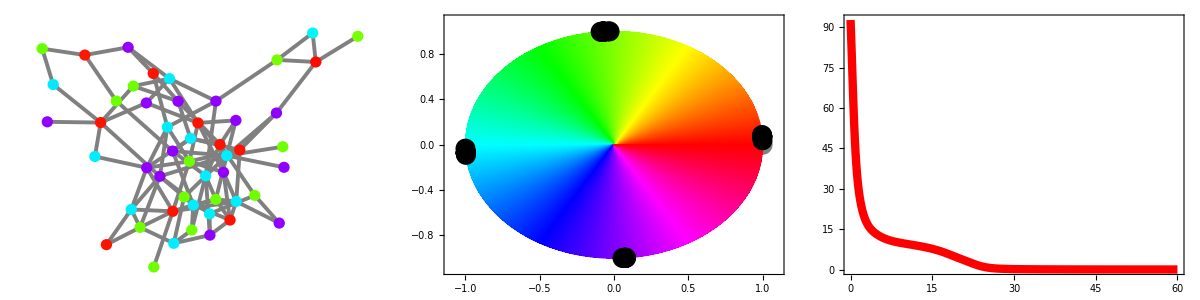

```mathematica
video[60]
```

```mathematica
simulaci1=Table[video[t],{t,0,60,0.05}];
```

```mathematica
Export["SM8.AVI",simulaci1]
```